```mathematica
none={33.8,32.9,39.3,37.7,37.6,61.6,45.7,36.8,15.2,36.,55.3,44.5,47.5,39.8,49.8,42.,0,0,33.3}/(1-.01{33.8,25.9,20.3,26.7,17.4,3.6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0.})
pure={19.9,28.1,24.3,17.3,24.7,8.7,15.2,17.6,30.4,28.7,11.3,37.4,33.6,49.7,45.6,50.7,0,0,6.1}/(1-.01{33.8,25.9,20.3,26.7,17.4,3.6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0.})
```

{51.0574,44.3995,49.3099,51.4325,45.5206,63.9004,45.7,36.8,15.2,36.,55.3,44.5,47.5,39.8,49.8,42.,0.,0.,33.3}

{30.0604,37.9217,30.4893,23.6016,29.9031,9.0249,15.2,17.6,30.4,28.7,11.3,37.4,33.6,49.7,45.6,50.7,0.,0.,6.1}

```mathematica
years=Range[2014,1996,-1]
```

{2014,2013,2012,2011,2010,2009,2008,2007,2006,2005,2004,2003,2002,2001,2000,1999,1998,1997,1996}

```mathematica
pairs=Select[Transpose[{years,none}],#[[2]]≠0&]
purepairs=Select[Transpose[{years,pure}],#[[2]]≠0&]
```

{{2014,51.0574},{2013,44.3995},{2012,49.3099},{2011,51.4325},{2010,45.5206},{2009,63.9004},{2008,45.7},{2007,36.8},{2006,15.2},{2005,36.},{2004,55.3},{2003,44.5},{2002,47.5},{2001,39.8},{2000,49.8},{1999,42.},{1996,33.3}}

{{2014,30.0604},{2013,37.9217},{2012,30.4893},{2011,23.6016},{2010,29.9031},{2009,9.0249},{2008,15.2},{2007,17.6},{2006,30.4},{2005,28.7},{2004,11.3},{2003,37.4},{2002,33.6},{2001,49.7},{2000,45.6},{1999,50.7},{1996,6.1}}

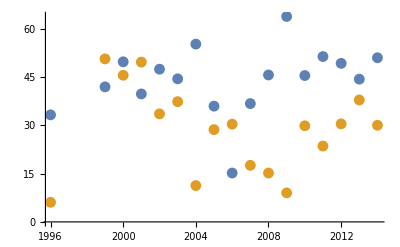

```mathematica
ListPlot[{pairs,purepairs}]
```

```mathematica
fit=Fit[pairs,{1,x},x]
purefit=Fit[purepairs,{1,x},x]
```

-1166.18+0.603417 x

828.747-0.398868 x

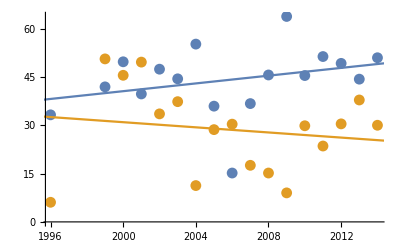

```mathematica
Show[ListPlot[{pairs,purepairs}],Plot[{fit,purefit},{x,1995,2015}]]
```